# Consumer-Resource Model with Type II to Type III Functional Response - Deterministic & Stochastic Models High Production Potential - K=7.3 Low Production Potential - K=1.2

## Model & Parameters

```mathematica
f1=( R1 r(1-R1/k))- (R1^(q+1) a C1/(b^(q+1)+R1^(q+1)));
f2= C1(e a R1^(q+1)/(b^(q+1)+R1^(q+1))-d);
```

```mathematica
Clear[param]
```

```mathematica
param=Dispatch[{
r-> 4.0, 
e-> 0.6,
b-> 3.2, 
q-> 1.0, 
k-> 1.2, 
a-> 4.2, 
d-> 0.5}
] ;
```

```mathematica
fChain[{R0_,C0_}]:=Module[{transform={R1->R1[t],C1->C1[t]}},
{R1'[t]==(f1/.transform),
C1'[t]==(f2/.transform),
R1[0]==R0,
C1[0]==C0}
]
```

```mathematica
tmax=3000;
```

## Deterministic Time Series

```mathematica
solu[spar_]:=NDSolve[fChain[{0.5,0.5}]/.spar/.param,{R1,C1},{t,0,tmax},AccuracyGoal->70,MaxStepSize->0.05,MaxSteps->500000];
```

```mathematica
Manipulate[
Plot[Evaluate[{R1[t],C1[t]}/.solu[{q-> qin, a-> ain,k -> kin,  r-> rin, e->ein,d->din/.b-> bin}]],{t,2900, 3000},PlotLegends->{"R","C"},Frame->True,PlotRange->{All,All}],
{{rin, 4.0}, 1.0, 5.0, Appearance -> "Labeled"}, 
{{kin, 1.2}, 0.0, 8.0, Appearance -> "Labeled"}, 
{{ain, 4.2},0.1,5.0,Appearance->"Labeled"},
{{ein,0.6},0.01,1.0, Appearance->"Labeled"},
{{din,0.5},0.0, 2.5,Appearance->"Labeled"}, 
{{qin,0.0}, 0.0,1.0, Appearance -> "Labeled"}, 
{{bin, 3.2}, 0.0, 10.0, Appearance-> "Labeled"}

]
```

## Stochastic Time Series

```mathematica
Clear[perturb]
perturb[sz_]=WhenEvent[Mod[t,1],
{R1[t]->If[R1[t]>0,Max[R1[t]+RandomVariate[NormalDistribution[0,sz]],0],0],
C1[t]->If[C1[t]>0,Max[C1[t]+RandomVariate[NormalDistribution[0,sz]],0],0]}
];
```

```mathematica
sol[spar_]:=NDSolve[{fChain[{0.5,0.5}]/.spar/.param,perturb[0.035]},{R1,C1},{t,0,tmax},AccuracyGoal->70,MaxStepSize->0.05,MaxSteps->500000];
```

```mathematica
Manipulate[
Plot[Evaluate[{R1[t],C1[t]}/.sol[{q-> qin, a-> ain,k -> kin,  r-> rin, e->ein,d->din/.b-> bin}]],{t,1000, 3000},PlotLegends->{"R","C"},Frame->True,PlotRange->{All,All}],
{{rin, 4.0}, 1.0, 5.0, Appearance -> "Labeled"}, 
{{kin, 1.2}, 0.0, 8.0, Appearance -> "Labeled"}, 
{{ain, 4.2},0.1,5.0,Appearance->"Labeled"},
{{ein,0.6},0.01,1.0, Appearance->"Labeled"},
{{din,0.5},0.0, 2.5,Appearance->"Labeled"}, 
{{qin,0.0}, 0.0,1.0, Appearance -> "Labeled"}, 
{{bin, 3.2}, 0.0, 5.0, Appearance-> "Labeled"}

]
```

#### Equilibrium Stability - Eigenvalues

```mathematica
jac=Outer[D,{f1,f2},{R1,C1}];
```

```mathematica
Simplify[jac]//MatrixForm;
```

```mathematica
equil=Solve[{f1==0,f2==0},{R1,C1}]
```

```mathematica
A=Table[jac/.equil[[i]],{i,3}];
```

```mathematica
Simplify[MatrixForm/@A//TableForm];
```

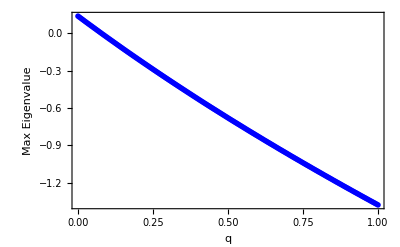

```mathematica
eigs=Table[{qval,Max[Re[Eigenvalues[jac/.equil[[3]]/.q-> qval/.param]]]},{qval,0.0,1.0,0.005}];
ListPlot[eigs,Frame->True,
Axes->True,
PlotStyle->Directive[Blue,PointSize[0.01]],
FrameLabel->{"q","Max Eigenvalue"},PlotRange->All]
```

#### Deterministic Model - Consumer Density

```mathematica
MeanCdet[par_]:=Mean[Flatten[C1[Range[(tmax-2900),tmax,0.01]]/.solu[par]]];
```

```mathematica
MeanCdetq=ParallelTable[{qin, MeanCdet[q-> qin] }, {qin, 0.0, 1.0, 0.005}];
```

```mathematica
flatMeanCqdet=Flatten [MeanCdetq];
```

```mathematica
ConsumerMeandet=Partition [flatMeanCqdet, 2];
```

```mathematica
ListLinePlot [ConsumerMeandet,  PlotRange->All,PlotStyle->{Gray,Thickness[.005]}]
```

```mathematica
ConsumerMeandet//TableForm;
```

#### Deterministic Model - Stability Figure

```mathematica
InteriorEqsQK[par1_,par2_]:=Select [NSolve[{f1==0,f2==0}/.par1/.par2/.param,{R1, C1}, WorkingPrecision->70],And@@Positive[#[[All,2]]]&]
```

```mathematica
jacQK[par1_,par2_]:=Outer[D,{f1,f2},{R1,C1}]/.par1/.par2/.param/.InteriorEqsQK[par1,par2]
```

```mathematica
MaxEigQK[par1_,par2_]:=Max[Re[Eigenvalues[jacQK[par1, par2]]]]
```

```mathematica
eigvalQK=ParallelTable[{{qin,kin}, MaxEigQK[q-> qin, k->kin] }, {qin, 0.0, 1.0, 0.05}, {kin, 0, 8, 0.05}];
```

```mathematica
flateigQK=Flatten [eigvalQK];
```

```mathematica
QK=Partition [flateigQK, 3];
```

```mathematica
QK//TableForm;
```

```mathematica
ListContourPlot[QK,Frame->True,
Axes->False,ColorFunction->"GrayTones", PerformanceGoal->"Quality",InterpolationOrder->Automatic,Contours-> {0},

FrameLabel->{Style["q",FontSize->14,Bold],Style["K",FontSize->14,Bold]},PlotLegends->Automatic,PlotRange->{{0.0,1.0},{0.0, 8.0}}]
```

```mathematica
Stochastic Model - Consumer Density
```

```mathematica
MeanC[par_]:=Mean[Flatten[C1[Range[(tmax-2900),tmax,0.01]]/.sol[par]]];
```

```mathematica
MeanCq=ParallelTable[{qin, MeanC[ q-> qin] }, {qin, 0.0, 1.0, 0.005}];
```

```mathematica
flatMeanCq=Flatten [MeanCq];
```

```mathematica
ConsumerMean=Partition [flatMeanCq, 2];
```

```mathematica
ListLinePlot [ConsumerMean,  PlotRange->All,PlotStyle->{Gray,Thickness[.005]}]
```

```mathematica
ConsumerMean//TableForm;
```

```mathematica
Stochastic Model - Consumer SD
```

```mathematica
SDC[par_]:=StandardDeviation[Flatten[C1[Range[(tmax-2900),tmax,0.01]]/.sol[par]]];
```

```mathematica
SDCq=ParallelTable[{qin, SDC[q-> qin] }, {qin, 0.0, 1.0, 0.005}];
```

```mathematica
flatSDCq=Flatten [SDCq];
```

```mathematica
ConsumerSD=Partition [flatSDCq, 2];
```

```mathematica
ListLinePlot [ConsumerSD,  PlotRange->All,PlotStyle->{Gray,Thickness[.005]}]
```

```mathematica
ConsumerSD//TableForm;
```

```mathematica
Cinter1=Interpolation[ConsumerSD];
Cinter2=Interpolation[ConsumerMean];
Plot[Cinter1[x]/Cinter2[x],{x,0,1.0},PlotStyle->{Gray,Thickness[.005]}]
```

```mathematica
CVC=Table[{x, Cinter1[x]/Cinter2[x] }, {x, 0.0, 1.0, 0.005}];
```

```mathematica
CVC//TableForm;
```

```mathematica
Stochastic Model - Persistence Figure
```

```mathematica
sol2[spar1_,spar2_]:=NDSolve[{fChain[{0.5,0.5}]/.spar1/.spar2/.param,perturb[0.035]},{R1,C1},{t,0,tmax},AccuracyGoal->70,MaxStepSize->0.05,MaxSteps->500000];
```

```mathematica
MeanConsumer[par1_,par2_]:=Mean[Flatten[C1[Range[(tmax-2900),tmax,0.01]]/.sol2[par1,par2]]];
```

```mathematica
MeanCqk=ParallelTable[{{qin,kin}, MeanConsumer[q-> qin, k->kin] }, {qin, 0.0, 1.0, 0.01}, {kin, 0.0, 8.0, 0.05}];
```

```mathematica
flatMeanCqk=Flatten [MeanCqk];
```

```mathematica
CqkMeanDen=Partition [flatMeanCqk, 3];
```

```mathematica
ListContourPlot[CqkMeanDen,Frame->True,
Axes->False, PerformanceGoal->"Quality",InterpolationOrder->Automatic,Contours-> {0.001},Mesh->None,ContourStyle->None,
FrameLabel->{Style["q",FontSize->14,Bold],Style["K",FontSize->14,Bold]},PlotLegends->Automatic,PlotTheme->{ "Monochrome"},PlotRange->{{0.0,1.0},{0.0, 8.0}}]
```

```mathematica
CqkMeanDen//TableForm;
```

```mathematica
Isoclines for Supplementary Material
```

```mathematica
Solve [f1==0, C1];
```

```mathematica
riso=-(r R1^-q (-k+R1) (b^(1+q)+R1^(1+q)))/(a k);
```

```mathematica
Solve[f2==0, R1];
```

```mathematica
ciso = (-(b^(-1-q) (d-a e))/d)^(1/(-1-q));
```

```mathematica
Show[
Plot[{riso/.param }, {R1,0, 8},
PlotRange->{{0,7.5},{0,7.0}},FrameLabel->{Style["Resource",FontSize->14,Bold],Style["Consumer",FontSize->14,Bold]},Frame->True, Axes -> True,PlotStyle->{RBGColor[0,1,0],Thickness[.01]}], Graphics[{Thick,Lighter[Orange],Line[{{ciso/.param,0},{ciso/.param,20}}
]}]]
```